# The sum of Lagrange numbers

```mathematica
SetDirectory[NotebookDirectory[]];
markovNums = ReadList["Markov20002.txt"];
S = 4-GoldenRatio-√2;
c=0.18071710471180647805779264904916762147630562767088273^(-.5);
M = 20000;
markovNums[[M]]
```

979132271585986692497592379008625942758512169481427182878112624062022223940144529631165216064142598364080873729797533629169026574366181289721922

```mathematica
Timing[remainders=Module[{R=S, res=Table[0, {M}]},For[j=1,j≤M,j++,R-= 3-√(9-4/markovNums[[j]]^2); res[[j]]= R];res];]
Block[{$MaxExtraPrecision=300}, Timing[remaindersN= N[remainders,10];]]
remaindersN[[M]]
```

{112.947,Null}

{7725.82,Null}

4.242079151×10^-287

```mathematica
expectedR[n_] := (6 √n)/c ⅇ^(-2c √n);
Timing[expected = Table[N[expectedR[n],10],{n,1,M}];]
expected[[M]]
```

{0.277069,Null}

4.00428×10^-287

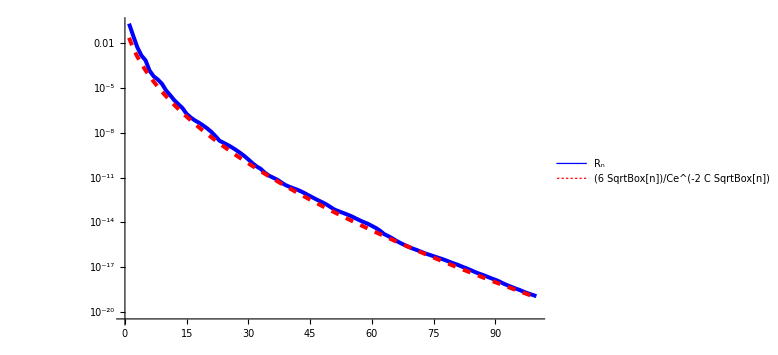

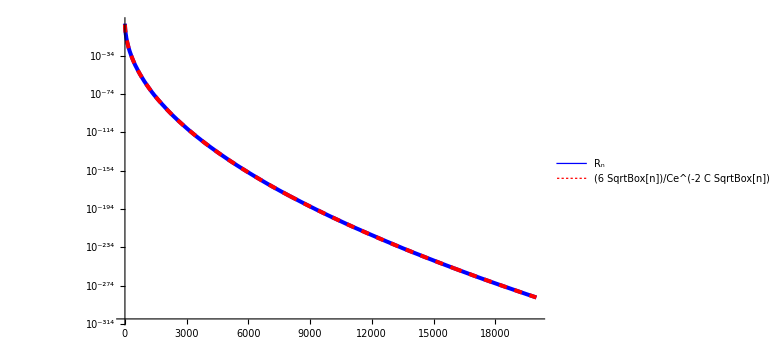

```mathematica
ListLogPlot[{remaindersN[[1;;100]],expected[[1;;100]]},Joined->True,PlotStyle->{{Joined,Blue, Thickness[0.005]},{Dashing[0.01],Red,  Thickness[0.005]}},PlotLegends->{"R_n","(6 SqrtBox[n])/Ce^(-2 C SqrtBox[n])"}, Ticks->{Automatic, Automatic}, ImageSize->Large]
ListLogPlot[{remaindersN[[1;;M]],expected[[1;;M]]},Joined->True,PlotStyle->{{Joined,Blue, Thickness[0.005]},{Dashing[0.01],Red,  Thickness[0.005]}},PlotLegends->{"R_n","(6 SqrtBox[n])/Ce^(-2 C SqrtBox[n])"}, Ticks->{Automatic, {{1,1}, {10^-100,"10^-100"}, {10^-200,"10^-200"}}}, ImageSize->Large]
```